```mathematica
G[x_,μ_,σ_]:=ⅇ^((-(x-μ)^2)/(2 σ^2));
```

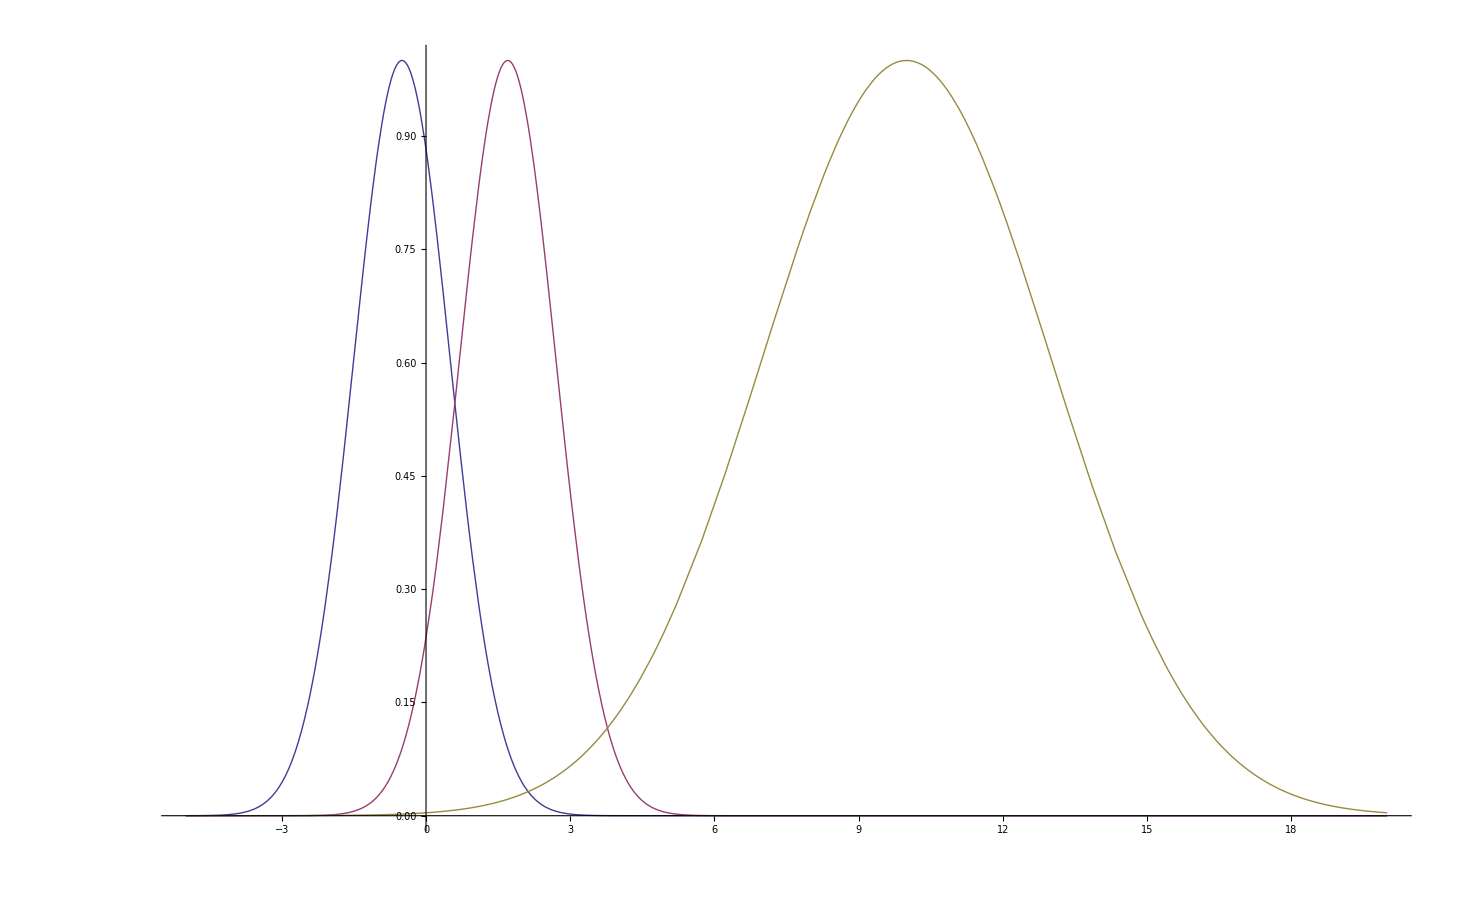

```mathematica
Plot[{G[x,-.5,1],G[x,1.7,1],G[x,10,3]},{x,-5,20},PlotRange->{0,1}]
```

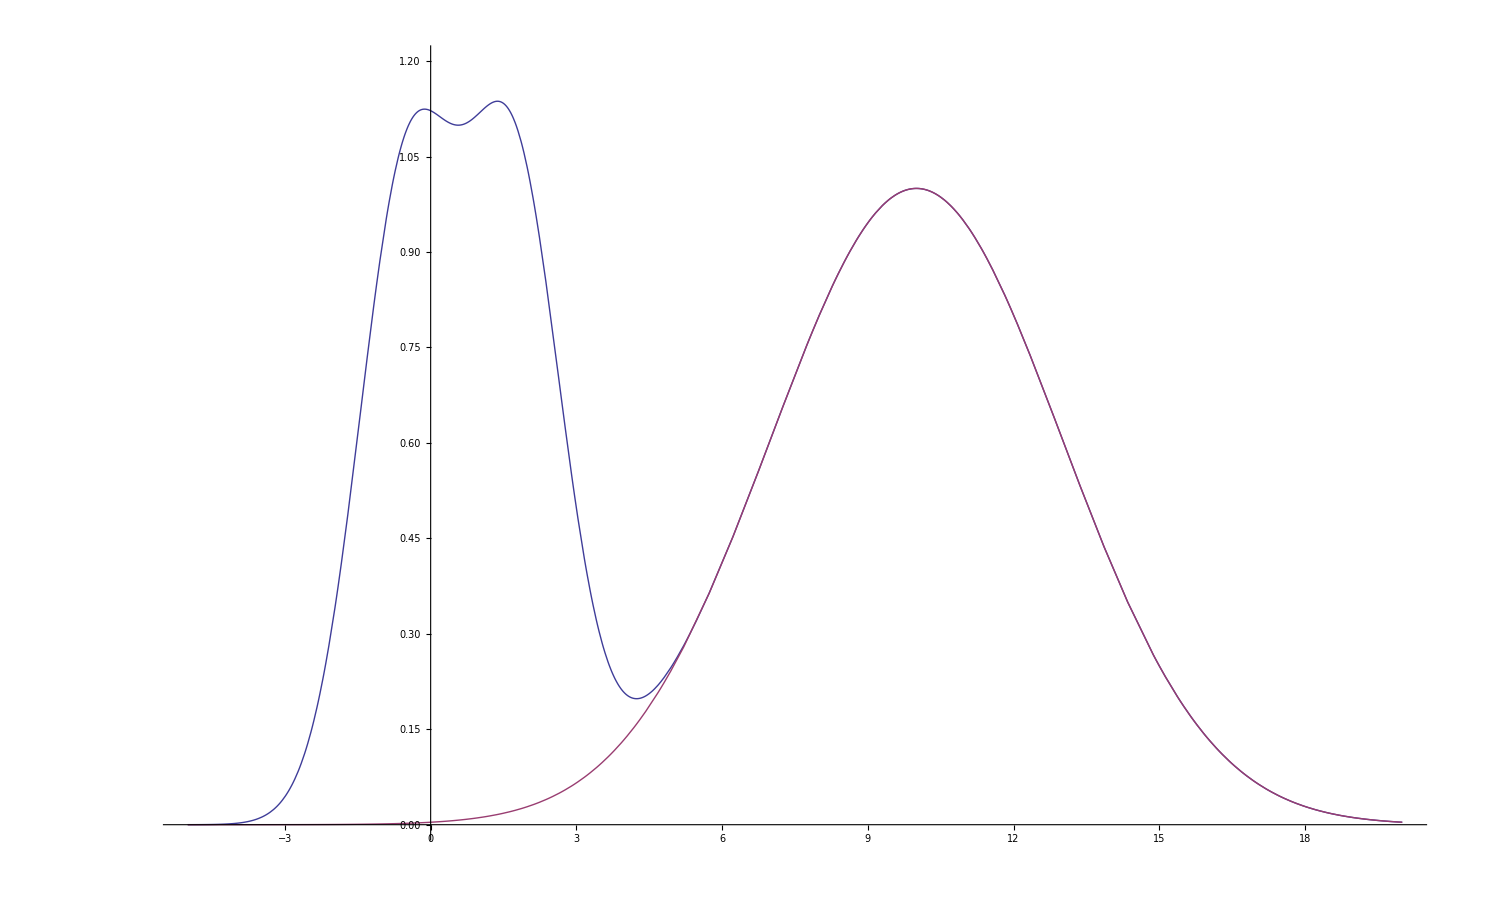

```mathematica
Plot[{G[x,-.5,1]+G[x,1.7,1]+G[x,10,3],G[x,10,3]},{x,-5,20},PlotRange->{0,1.2}]
```